# Square Antiprism Modelling - Over-constrained Approach

```mathematica
(* Define the initial points *)
a = {0, 0, 0};
b = {1, 0, 0};
c = {1, 1, 0};
d = {0, 1, 0};

maxAngle = 360;

(* Function to solve for F, G and H given an angle, side is the length of the triangles, defaults to equalateral, top is the length of top trusses, defaults to 1*)
solvePoints[angle_, side_:1] := Module[{
        e, sol, solPoints, height
    },
    
    height = Sqrt[side^2 - (1/2)^2];
    
	e = RotationMatrix[angle, {1, 0, 0}] . {1/2, 0, height};
    sol = TimeConstrained[NSolve[
    {
      (*For point F*)
      Sqrt[(e[[1]] - fx)^2 + (e[[2]] - fy)^2 + (e[[3]] - fz)^2] == 1, (*E-F*)
      Sqrt[(b[[1]] - fx)^2 + (b[[2]] - fy)^2 + (b[[3]] - fz)^2] == side, (*B-F*)
      Sqrt[(c[[1]] - fx)^2 + (c[[2]] - fy)^2 + (c[[3]] - fz)^2] == side, (*C-F*)
      (*For point G*)
      Sqrt[(fx - gx)^2 + (fy - gy)^2 + (fz - gz)^2] == 1, (*F-G*)
      Sqrt[(c[[1]] - gx)^2 + (c[[2]] - gy)^2 + (c[[3]] - gz)^2] == side, (*C-G*)
      Sqrt[(d[[1]] - gx)^2 + (d[[2]] - gy)^2 + (d[[3]] - gz)^2] == side, (*D-G*)
      (*For point H*)
      Sqrt[(gx - hx)^2 + (gy - hy)^2 + (gz - hz)^2] == 1, (*G-H*)
      Sqrt[(a[[1]] - hx)^2 + (a[[2]] - hy)^2 + (a[[3]] - hz)^2] == side, (*A-H*)
      Sqrt[(d[[1]] - hx)^2 + (d[[2]] - hy)^2 + (d[[3]] - hz)^2] == side, (*D-H*)
      Sqrt[(e[[1]] - hx)^2 + (e[[2]] - hy)^2 + (e[[3]]- hz)^2] == 1 (*E-H*)
    }, 
    {fx, fy, fz, gx, gy, gz, hx, hy, hz}
    ],2,(* time limit in seconds *)
    {} (*fall back, return empty list*)
    ];
	
	(* Check if solutions were found *)
    If[Length[sol] > 0,
        solPoints = {fx, fy, fz, gx, gy, gz, hx, hy, hz} /. sol;
        (* Add E point values to each solution *)
        solPoints = Join[#, e] & /@ solPoints;
        solPoints,
        (* Return an empty list if no solutions are found *)
        {}
    ]
];

closestSolution[prevSolution_, curSolutions_] := Module[
    {distances, indexOfClosest, closest},
    
    (* Calculate the pairwise distances *)
    distances = EuclideanDistance[prevSolution, #] & /@ curSolutions;
    
    (* Find the index of the closest solution *)
    indexOfClosest = Ordering[distances, 1][[1]];
    
    (* Get the closest solution *)
    closest = curSolutions[[indexOfClosest]];
    
    Return[closest]
];

(*get trajectory of model based on an initial starting preference (iterates choosing closest next solution) *)
getTrajectory[baseStart_,angleMax_] := Module[
	{sum, trajectories, prevSolution, nextSolution},
	
	trajectories = {baseStart};
	prevSolution = baseStart;
	
	Monitor[
		For[angle = 1, angle <= angleMax, angle++,
			curSolution = solvePoints[angle*2Pi/360];
			(* Check if solutions were found *)
			If[Length[curSolution] > 0,
				(*Get next closest solution*)
				nextSolution = closestSolution[prevSolution,solvePoints[angle*2Pi/360]];
				(*set new solution as old for next iteration*)
				prevSolution = nextSolution;
				(*update trajectories*)
				trajectories = Append[trajectories, nextSolution],Continue[]]
		],
		ProgressIndicator[angle, {1, angleMax}]
	];
	
	Return[trajectories] 
];
```

### Animate Sample Trajectory

```mathematica
(*Get trajectories*)
trajectories = getTrajectory[solvePoints[0][[4]],maxAngle];

(* Filter out complex results *)
validTrajectories = Select[trajectories, FreeQ[#, _Complex] &];

(*Check if there are any valid trajectories*)
If[Length[validTrajectories] == 0, 
  Print["No valid trajectories found."];
  Return[]
];

fTrajectory = validTrajectories[[All, {1,2,3}]];
gTrajectory = validTrajectories[[All, {4,5,6}]];
hTrajectory = validTrajectories[[All, {7,8,9}]];
eTrajectory = validTrajectories[[All, {10,11,12}]];

(* Create the animation with only one point from each trajectory shown at a time *)
frames = Table[
  Module[{lines, validFrame = True},

    (* Ensure all points in the current frame are defined and valid *)
    If[!VectorQ[eTrajectory[[i]], NumericQ] || !VectorQ[fTrajectory[[i]], NumericQ] ||
       !VectorQ[gTrajectory[[i]], NumericQ] || !VectorQ[hTrajectory[[i]], NumericQ],
      validFrame = False;
    ];

    (* Only create the frame if all points are valid *)
    If[validFrame,
      lines = {
        {a, b}, {b, c}, {c, d}, {d, a}, 
        {eTrajectory[[i]], fTrajectory[[i]]}, {fTrajectory[[i]], gTrajectory[[i]]}, {gTrajectory[[i]], hTrajectory[[i]]}, {hTrajectory[[i]], eTrajectory[[i]]},
        {a, hTrajectory[[i]]}, {a, eTrajectory[[i]]}, {b, eTrajectory[[i]]}, {b, fTrajectory[[i]]}, 
        {c, fTrajectory[[i]]}, {c, gTrajectory[[i]]}, {d, gTrajectory[[i]]}, {d, hTrajectory[[i]]}, {d, eTrajectory[[i]]}
      };
      Graphics3D[{
        {Red, PointSize[Medium], Point[fTrajectory[[i]]]},
        {Green, PointSize[Medium], Point[gTrajectory[[i]]]},
        {Blue, PointSize[Medium], Point[hTrajectory[[i]]]},
        {Brown, PointSize[Medium], Point[eTrajectory[[i]]]},
        
        {Red, Line[Take[fTrajectory, i]]},
        {Green, Line[Take[gTrajectory, i]]},
        {Blue, Line[Take[hTrajectory, i]]},
        {Brown, Line[Take[eTrajectory, i]]},
        
        (* Add the original points *)
        {Black, PointSize[Large], Point[a]},
        {Black, PointSize[Large], Point[b]},
        {Black, PointSize[Large], Point[c]},
        {Black, PointSize[Large], Point[d]},
        
        (* Add lines between points *)
        Line[lines]
      }, Axes -> True, 
      AxesLabel -> {"x", "y", "z"}, 
      PlotRange -> {{-1, 2}, {-1, 2}, {-1, 2}}], (* Set fixed range *)
      (* Fallback in case of invalid frame *)
      Graphics3D[{}, Axes -> True, AxesLabel -> {"x", "y", "z"}, PlotRange -> {{-1, 2}, {-1, 2}, {-1, 2}}]
    ]
  ], {i, 1, Length[fTrajectory]}
];

(* Display the animation *)
ListAnimate[frames, ControlPlacement -> Top]

(* Save the animation as a GIF *)
Export["Desktop/trajectory_animation4.gif", frames, "DisplayDurations" -> 0.1]
```

$Aborted

Select::normal: Select[trajectories,FreeQ[#1,_Complex]&]で1の位置に原子的ではない式が想定されます．

Part::partd: 部分指定Select[trajectories,FreeQ[#1,_Complex]&]⟦All,{1,2,3}⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定Select[trajectories,FreeQ[#1,_Complex]&]⟦All,{4,5,6}⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定Select[trajectories,FreeQ[#1,_Complex]&]⟦All,{7,8,9}⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定Select[trajectories,FreeQ[#1,_Complex]&]⟦All,{10,11,12}⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定Select[trajectories,FreeQ[#1,_Complex]&]⟦All,{1,2,3}⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定Select[trajectories,FreeQ[#1,_Complex]&]⟦All,{4,5,6}⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定Select[trajectories,FreeQ[#1,_Complex]&]⟦All,{7,8,9}⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Desktop/trajectory_animation4.gif

### Find all Trajectories from Initial Starting Point (Very Slow)

```mathematica
For[i = 1, i < Dimensions[solvePoints[0]][[1]], i++,
  (*Get trajectories*)
  trajectories = getTrajectory[solvePoints[0][[i]], maxAngle];
  Print["Step: ", i, " of:", Dimensions[solvePoints[0]][[1]]];
  (* Filter out complex results *)
  validTrajectories = Select[trajectories, FreeQ[#, _Complex] &];
  (*Print["Valid Trajectories ", i, ": ", validTrajectories];*)
  
 (* Print["fTrajectory ", i, ": ", validTrajectories[[All, {1,2,3}]]]; *)
  
  (*Check if there are any valid trajectories*)
  If[Length[validTrajectories] == 0, 
    Print["No valid trajectories found."];
    Return[]
  ];
  
  If[i == 1, 
    fTrajectory = validTrajectories[[All, {1,2,3}]];
    gTrajectory = validTrajectories[[All, {4,5,6}]];
    hTrajectory = validTrajectories[[All, {7,8,9}]];
    eTrajectory = validTrajectories[[All, {10,11,12}]],
    (*Else, add trajectories onto current ones*)
    fTrajectory = Join[fTrajectory, validTrajectories[[All, {1,2,3}]]];
    gTrajectory = Join[gTrajectory, validTrajectories[[All, {4,5,6}]]];
    hTrajectory = Join[hTrajectory, validTrajectories[[All, {7,8,9}]]];
    eTrajectory = Join[eTrajectory, validTrajectories[[All, {10,11,12}]]];
  ];
]

Print["Length of fTrajectory: ", Length[fTrajectory]];
(*Print["Total fTrajectory: ", fTrajectory];*)
```

### Find all Solutions at Each Interval (Faster)

```mathematica
getSolutions[angleMax_,interval_,side_:1] := Module[
	{solutions},
	
	solutions = {};
	
	Monitor[
		For[angle = 0, angle <= angleMax, angle = angle + interval,
			curSolutions = solvePoints[angle*2Pi/360,side];
			(* Check if solutions were found *)
			If[Length[curSolution] > 0,
				(*update trajectories*)
				solutions = Join[solutions, curSolutions],
				(*else skip to next angle*)
				Continue[]]
		],
		ProgressIndicator[angle, {1, angleMax}]
	];
	
	Return[solutions] 
	
];

solutions = getSolutions[360,1,1];
```

### Find Valid Solutions

```mathematica
Dimensions[solutions]
validSolutions = Select[solutions, FreeQ[#, _Complex] &];
Dimensions[validSolutions]

fTrajectory = validSolutions[[All, {1,2,3}]];
gTrajectory = validSolutions[[All, {4,5,6}]];
hTrajectory = validSolutions[[All, {7,8,9}]];
eTrajectory = validSolutions[[All, {10,11,12}]];
```

{2062,12}

{1450,12}

### Calculate Angles from Each Trajectory List

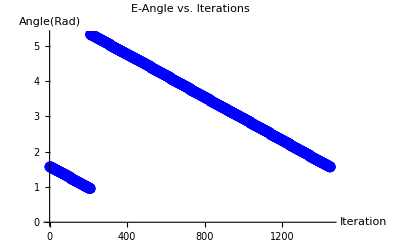

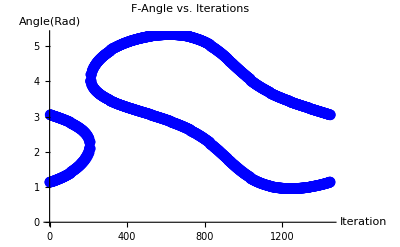

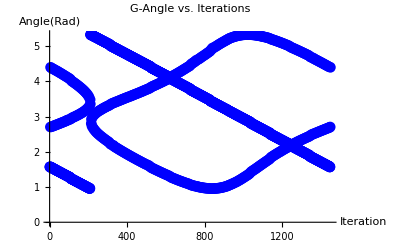

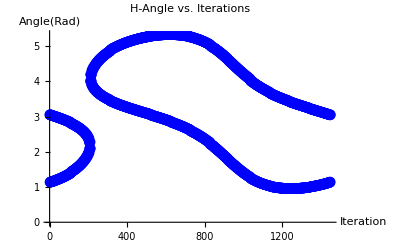

```mathematica
(*Ensuring lengths are equal*)
Length[fTrajectory] ==  Length[gTrajectory] == Length[hTrajectory] == Length[eTrajectory];

(*Normalise trajectories (centering)*)
eTrajectoryCentred = Map[# - {1/2,0,0} &, eTrajectory];
fTrajectoryCentred = Map[# - {1,1/2,0} &, fTrajectory];
gTrajectoryCentred = Map[# - {1/2,1,0} &, gTrajectory];
hTrajectoryCentred = Map[# - {0,1/2,0} &, hTrajectory];

(*Get angles for points*)

eAngles = {}; (*Point E*)
For[i = 1, i < Length[eTrajectoryCentred],i++,
	curAngle = ArcTan[-eTrajectoryCentred[[i]][[2]],eTrajectoryCentred[[i]][[3]]];	
	If[curAngle < 0, curAngle = curAngle + 2Pi];
	eAngles = Append[eAngles, curAngle];
];

fAngles = {}; (*Point F*)
For[i = 1, i < Length[fTrajectoryCentred],i++,
	curAngle = ArcTan[fTrajectoryCentred[[i]][[1]],fTrajectoryCentred[[i]][[3]]];	
	If[curAngle < 0, curAngle = curAngle + 2Pi];
	fAngles = Append[fAngles, curAngle];
];

gAngles = {}; (*Point G*)
For[i = 1, i < Length[gTrajectoryCentred],i++,
	curAngle = ArcTan[gTrajectoryCentred[[i]][[2]],gTrajectoryCentred[[i]][[3]]];	
	If[curAngle < 0, curAngle = curAngle + 2Pi];
	gAngles = Append[gAngles, curAngle];
];

hAngles = {}; (*Point H*)
For[i = 1, i < Length[hTrajectoryCentred],i++,
	curAngle = ArcTan[-hTrajectoryCentred[[i]][[1]],hTrajectoryCentred[[i]][[3]]];	
	If[curAngle < 0, curAngle = curAngle + 2Pi];
	hAngles = Append[hAngles, curAngle];
];



(*Plot Angles*)
ListPlot[eAngles, PlotMarkers -> Automatic, PlotStyle -> Blue, 
 AxesLabel -> {"Iteration", "Angle(Rad)"}, 
 PlotLabel -> "E-Angle vs. Iterations"]

ListPlot[fAngles, PlotMarkers -> Automatic, PlotStyle -> Blue, 
 AxesLabel -> {"Iteration", "Angle(Rad)"}, 
 PlotLabel -> "F-Angle vs. Iterations"]

ListPlot[gAngles, PlotMarkers -> Automatic, PlotStyle -> Blue, 
 AxesLabel -> {"Iteration", "Angle(Rad)"}, 
 PlotLabel -> "G-Angle vs. Iterations"]

ListPlot[hAngles, PlotMarkers -> Automatic, PlotStyle -> Blue, 
 AxesLabel -> {"Iteration", "Angle(Rad)"}, 
 PlotLabel -> "H-Angle vs. Iterations"]
```

### Compare Angle Combinations

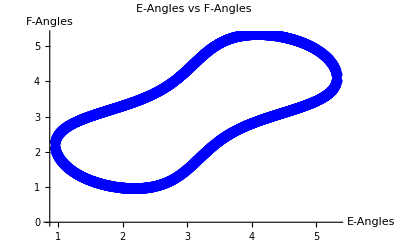

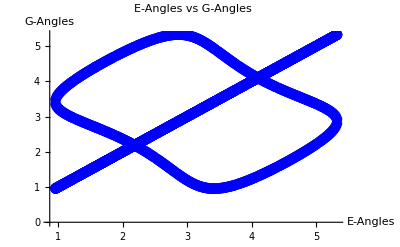

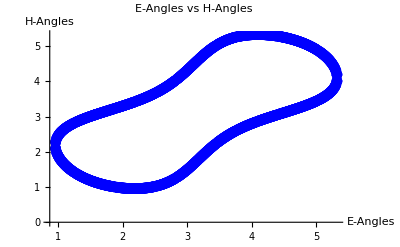

-Graphics3D-

```mathematica
(* Combine the angle values into pairs *)
efData = Transpose[{eAngles, fAngles}];
egData = Transpose[{eAngles, gAngles}];
ehData = Transpose[{eAngles, hAngles}];
fghData= Transpose[{fAngles, gAngles, hAngles}];

(* Plot the paired values *)
ListPlot[efData, PlotMarkers -> Automatic, PlotStyle -> Blue, 
 AxesLabel -> {"E-Angles", "F-Angles"}, 
 PlotLabel -> "E-Angles vs F-Angles"]

ListPlot[egData, PlotMarkers -> Automatic, PlotStyle -> Blue, 
 AxesLabel -> {"E-Angles", "G-Angles"}, 
 PlotLabel -> "E-Angles vs G-Angles"]

ListPlot[ehData, PlotMarkers -> Automatic, PlotStyle -> Blue, 
 AxesLabel -> {"E-Angles", "H-Angles"}, 
 PlotLabel -> "E-Angles vs H-Angles"]
 
ListPointPlot3D[fghData, PlotStyle -> Blue, 
 AxesLabel -> {"F-Angles", "G-Angles", "H-Angles"}, 
 PlotLabel -> "3D Plot of F G H Angles"]
```

### View 4D of all angles onto a 2D plane (Oblique projection)

```mathematica
allData = Transpose[{eAngles, fAngles, gAngles, hAngles}];
Dimensions[allData];
theta = 60 * 2Pi/360;
obliqueProjection = {{1,0,0,Cos[theta]},
					{0,1,0,Sin[theta]},
					{0,0,1,Cos[theta]}};

obliqueData = obliqueProjection . Transpose[allData];
Dimensions[obliqueData];

ListPointPlot3D[Transpose[obliqueData], PlotStyle -> Blue, 
 AxesLabel -> {"", "", ""}, 
 PlotLabel -> "Oblique Projection of All Angles"]
```

-Graphics3D-

### See How Angles Behave with Changed Side Lengths

```mathematica
sideValues = Table[i, {i, 0.6, 2.0, 0.05}];

(* Create the animation *)
frames = Monitor[
  Table[
    solutions = getSolutions[360, 1, sideValue];
    validSolutions = Select[solutions, FreeQ[#, _Complex] &];

    fTrajectory = validSolutions[[All, {1, 2, 3}]];
    gTrajectory = validSolutions[[All, {4, 5, 6}]];
    hTrajectory = validSolutions[[All, {7, 8, 9}]];
    eTrajectory = validSolutions[[All, {10, 11, 12}]];

    (* Normalize trajectories (centering) *)
    eTrajectoryCentred = Map[# - {1/2, 0, 0} &, eTrajectory];
    fTrajectoryCentred = Map[# - {1, 1/2, 0} &, fTrajectory];
    gTrajectoryCentred = Map[# - {1/2, 1, 0} &, gTrajectory];
    hTrajectoryCentred = Map[# - {0, 1/2, 0} &, hTrajectory];

    (* Get angles for points *)
    eAngles = {}; (* Point E *)
    For[i = 1, i < Length[eTrajectoryCentred], i++,
      curAngle = ArcTan[-eTrajectoryCentred[[i]][[2]], eTrajectoryCentred[[i]][[3]]];
      If[curAngle < 0, curAngle = curAngle + 2 Pi];
      eAngles = Append[eAngles, curAngle];
    ];

    fAngles = {}; (* Point F *)
    For[i = 1, i < Length[fTrajectoryCentred], i++,
      curAngle = ArcTan[fTrajectoryCentred[[i]][[1]], fTrajectoryCentred[[i]][[3]]];
      If[curAngle < 0, curAngle = curAngle + 2 Pi];
      fAngles = Append[fAngles, curAngle];
    ];

	gAngles = {}; (*Point G*)
	For[i = 1, i < Length[gTrajectoryCentred],i++,
		curAngle = ArcTan[gTrajectoryCentred[[i]][[2]],gTrajectoryCentred[[i]][[3]]];	
		If[curAngle < 0, curAngle = curAngle + 2Pi];
		gAngles = Append[gAngles, curAngle];
	];
	
	hAngles = {}; (*Point H*)
	For[i = 1, i < Length[hTrajectoryCentred],i++,
		curAngle = ArcTan[-hTrajectoryCentred[[i]][[1]],hTrajectoryCentred[[i]][[3]]];	
		If[curAngle < 0, curAngle = curAngle + 2Pi];
		hAngles = Append[hAngles, curAngle];
	];

	allData = Transpose[{eAngles, fAngles, gAngles, hAngles}];
	Dimensions[allData];
	theta = 60 * 2Pi/360;
	obliqueProjection = {{1,0,0,Cos[theta]},
						{0,1,0,Sin[theta]},
						{0,0,1,Cos[theta]}};
	
	obliqueData = obliqueProjection . Transpose[allData];
	Dimensions[obliqueData];
	
	ListPointPlot3D[Transpose[obliqueData], PlotStyle -> Blue, 
	 PlotRange -> {{0, 4 Pi}, {0, 4 Pi}, {0, 4 Pi}},
	 AxesLabel -> {"", "", ""}, 
	 PlotLabel -> "Oblique Projection of All Angles"]

(*    (* Combine the angle values into pairs *)
    efData = Transpose[{eAngles, fAngles}];

    (* Plot the paired values *)
    ListPlot[efData, PlotMarkers -> Automatic, PlotStyle -> Blue,
     PlotRange -> {{0, 2 Pi}, {0, 2 Pi}},
     AxesLabel -> {"E-Angles", "F-Angles"},
     PlotLabel -> "E-Angles vs F-Angles"]*)
    ,
    {sideValue, sideValues}
  ],
  ProgressIndicator[Dynamic[sideValue], {Min[sideValues], Max[sideValues]}]
];

ListAnimate[frames, AnimationRate -> 10, DefaultDuration -> 5]
```

```mathematica
(* Save the animation as a GIF *)
Export["Desktop/All Angles Angles with Side Change.gif", frames, "DisplayDurations" -> 0.1]
```

Desktop/All Angles Angles with Side Change.gif